1.4

15

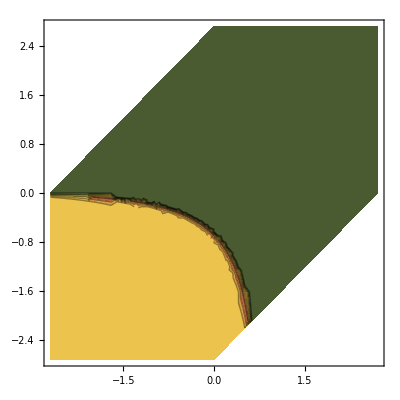

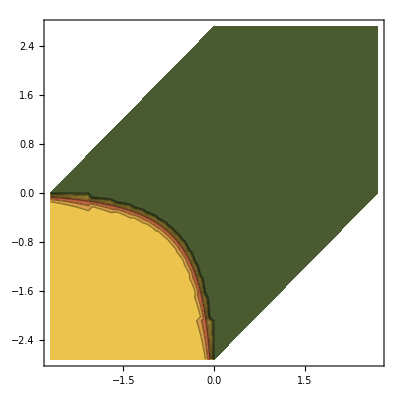

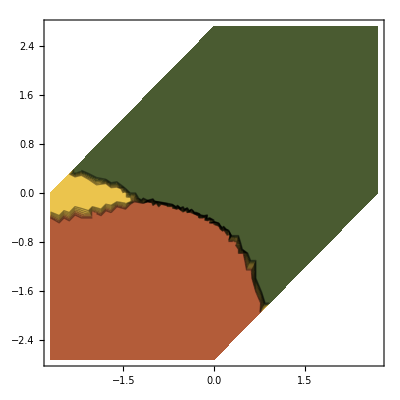

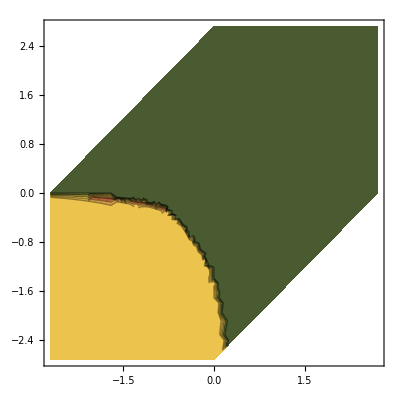

```mathematica
d=1.4
n=15


Borda=Table[0,{i,n},{j,n},{k,n}];
(*Condorcet=Table[0,{i,n},{j,n},{k,n}];*)
Vecinski=Table[0,{i,n},{j,n},{k,n}];
GdK=Table[0,{i,n},{j,n},{k,n}];
TNdK=Table[0,{i,n},{j,n},{k,n}];

For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
For[k=1,k<n+1,k++,
alfa={i,j,0,0,0,k};

(*Borda*)
BoA=2*(alfa[[1]]+alfa[[4]])+alfa[[2]]+alfa[[5]];
BoB=2*(alfa[[3]]+alfa[[5]])+alfa[[1]]+alfa[[6]];
BoC=2*(alfa[[2]]+alfa[[6]])+alfa[[3]]+alfa[[4]];
Which[And[BoA>BoB,BoA>BoC],Borda[[i,j,k]]=1,And[BoB>BoA,BoB>BoC],Borda[[i,j,k]]=2,And[BoC>BoA,BoC>BoB],Borda[[i,j,k]]=3,True,Borda[[i,j,k]]=0];

(*Condorcet*)
(*ConAB=alfa[[1]]+alfa[[2]]+alfa[[4]]-(alfa[[3]]+alfa[[5]]+alfa[[6]]);
ConAC=alfa[[1]]+alfa[[4]]+alfa[[5]]-(alfa[[2]]+alfa[[3]]+alfa[[6]]);
ConBC=alfa[[1]]+alfa[[3]]+alfa[[5]]-(alfa[[2]]+alfa[[4]]+alfa[[6]]);
Which[And[ConAB>0,ConAC>0],Condorcet[[i,j,k]]=1,And[ConAB<0,ConBC>0],Condorcet[[i,j,k]]=2,And[ConAC<0,ConBC<0],Condorcet[[i,j,k]]=3,True,Condorcet[[i,j,k]]=0];*)

(*Vecinski*)
VeA=alfa[[1]]+alfa[[4]];
VeB=alfa[[3]]+alfa[[5]];
VeC=alfa[[2]]+alfa[[6]];
Which[And[VeA>VeB,VeA>VeC],Vecinski[[i,j,k]]=1,And[VeB>VeA,VeB>VeC],Vecinski[[i,j,k]]=2,And[VeC>VeA,VeC>VeB],Vecinski[[i,j,k]]=3,True,Vecinski[[i,j,k]]=0];


(*GdK*)
GdKA=alfa[[2]]+alfa[[5]]+(alfa[[3]]+alfa[[6]])*2^d;
GdKB=alfa[[1]]+alfa[[6]]+(alfa[[2]]+alfa[[4]])*2^d;
GdKC=alfa[[3]]+alfa[[4]]+(alfa[[1]]+alfa[[5]])*2^d;
Which[And[GdKA<GdKB,GdKA<GdKC],GdK[[i,j,k]]=1,And[GdKB<GdKA,GdKB<GdKC],GdK[[i,j,k]]=2,And[GdKC<GdKA,GdKC<GdKB],GdK[[i,j,k]]=3,True,GdK[[i,j,k]]=0];

(*TNdK*)
MdK={{alfa[[2]]+alfa[[5]]+(alfa[[3]]+alfa[[6]])*2^d,alfa[[1]]+alfa[[3]]+alfa[[4]]+alfa[[6]],alfa[[2]]+alfa[[5]]+(alfa[[1]]+alfa[[4]])*2^d},{alfa[[1]]+alfa[[6]]+(alfa[[2]]+alfa[[4]])*2^d,alfa[[2]]+alfa[[3]]+alfa[[4]]+alfa[[5]],alfa[[1]]+alfa[[6]]+(alfa[[3]]+alfa[[5]])*2^d},{alfa[[3]]+alfa[[4]]+(alfa[[1]]+alfa[[5]])*2^d,alfa[[1]]+alfa[[2]]+alfa[[5]]+alfa[[6]],alfa[[3]]+alfa[[4]]+(alfa[[2]]+alfa[[6]])*2^d}}; 
TNdKABC=MdK[[1,1]]+MdK[[2,2]]+MdK[[3,3]];
TNdKACB=MdK[[1,1]]+MdK[[2,3]]+MdK[[3,2]];
TNdKBAC=MdK[[1,2]]+MdK[[2,1]]+MdK[[3,3]];
TNdKBCA=MdK[[1,3]]+MdK[[2,1]]+MdK[[3,2]];
TNdKCAB=MdK[[1,2]]+MdK[[2,3]]+MdK[[3,1]];
TNdKCBA=MdK[[1,3]]+MdK[[2,2]]+MdK[[3,1]];
Which[And[TNdKABC<TNdKACB,TNdKABC<TNdKBAC,TNdKABC<TNdKBCA,TNdKABC<TNdKCAB,TNdKABC<TNdKCBA],TNdK[[i,j,k]]=1,And[TNdKACB<TNdKABC,TNdKACB<TNdKBAC,TNdKACB<TNdKBCA,TNdKACB<TNdKCAB,TNdKACB<TNdKCBA],TNdK[[i,j,k]]=1,And[TNdKBAC<TNdKABC,TNdKBAC<TNdKACB,TNdKBAC<TNdKBCA,TNdKBAC<TNdKCAB,TNdKBAC<TNdKCBA],TNdK[[i,j,k]]=2,And[TNdKBCA<TNdKABC,TNdKBCA<TNdKACB,TNdKBCA<TNdKBAC,TNdKBCA<TNdKCAB,TNdKBCA<TNdKCBA],TNdK[[i,j,k]]=2,And[TNdKCAB<TNdKABC,TNdKCAB<TNdKACB,TNdKCAB<TNdKBAC,TNdKCAB<TNdKBCA,TNdKCAB<TNdKCBA],TNdK[[i,j,k]]=3,And[TNdKCBA<TNdKABC,TNdKCBA<TNdKACB,TNdKCBA<TNdKBAC,TNdKCBA<TNdKBCA,TNdKCBA<TNdKCAB],TNdK[[i,j,k]]=3,True,TNdK[[i,j,k]]=0];

]]]

MatrixForm[Borda];
(*MatrixForm[Condorcet];*)
(*MatrixForm[Vecinski];*)
MatrixForm[GdK];
MatrixForm[TNdK];

f=ColorData["SandyTerrain"];

(*CRTANJE BORDA*)
BordaRez=Table[{0,0,0},{i,n^3}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
For[k=1,k<n+1,k++,
BordaRez[[(i-1)*n^2+(j-1)*n+k,1]]=Log[j/i];
BordaRez[[(i-1)*n^2+(j-1)*n+k,2]]=Log[k/i];
BordaRez[[(i-1)*n^2+(j-1)*n+k,3]]=Borda[[i,j,k]]
]]]
BordaRez=DeleteDuplicates[BordaRez];
(*ListPlot3D[BordaRez,PlotRange->{0,3},Ticks->{Automatic,Automatic,{1,2,3}},PlotLabel->"Borda izračun",ImageSize->Large]*)
ListContourPlot[BordaRez,ColorFunction->f]

(*CRTANJE Condorcet*)
(*CondorcetRez=Table[{0,0,0},{i,n^3}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
For[k=1,k<n+1,k++,
CondorcetRez[[(i-1)*n^2+(j-1)*n+k,1]]=Log[j/i];
CondorcetRez[[(i-1)*n^2+(j-1)*n+k,2]]=Log[k/i];
CondorcetRez[[(i-1)*n^2+(j-1)*n+k,3]]=Condorcet[[i,j,k]]
]]]
CondorcetRez=DeleteDuplicates[CondorcetRez];
ListPlot3D[CondorcetRez,PlotRange->{0,3},Ticks->{Automatic,Automatic,{1,2,3}},PlotLabel->"Condorcet izračun",ImageSize->Large]
ListContourPlot[CondorcetRez,ColorFunction->f]*)

(*CRTANJE Vecinski*)
VecinskiRez=Table[{0,0,0},{i,n^3}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
For[k=1,k<n+1,k++,
VecinskiRez[[(i-1)*n^2+(j-1)*n+k,1]]=Log[j/i];
VecinskiRez[[(i-1)*n^2+(j-1)*n+k,2]]=Log[k/i];
VecinskiRez[[(i-1)*n^2+(j-1)*n+k,3]]=Vecinski[[i,j,k]]
]]]
VecinskiRez=DeleteDuplicates[VecinskiRez];
(*ListPlot3D[VecinskiRez,PlotRange->{0,3},Ticks->{Automatic,Automatic,{1,2,3}},PlotLabel->"Vecinski izračun",ImageSize->Large]*)
ListContourPlot[VecinskiRez,ColorFunction->f]

(*CRTANJE GdK*)
GdKRez=Table[{0,0,0},{i,n^3}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
For[k=1,k<n+1,k++,
GdKRez[[(i-1)*n^2+(j-1)*n+k,1]]=Log[j/i];
GdKRez[[(i-1)*n^2+(j-1)*n+k,2]]=Log[k/i];
GdKRez[[(i-1)*n^2+(j-1)*n+k,3]]=GdK[[i,j,k]]
]]]
GdKRez=DeleteDuplicates[GdKRez];
(*ListPlot3D[GdKRez,PlotRange->{0,3},Ticks->{Automatic,Automatic,{1,2,3}},PlotLabel->"GdK izračun",ImageSize->Large]*)
ListContourPlot[GdKRez,ColorFunction->f]

(*CRTANJE TNdK*)
TNdKRez=Table[{0,0,0},{i,n^3}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
For[k=1,k<n+1,k++,
TNdKRez[[(i-1)*n^2+(j-1)*n+k,1]]=Log[j/i];
TNdKRez[[(i-1)*n^2+(j-1)*n+k,2]]=Log[k/i];
TNdKRez[[(i-1)*n^2+(j-1)*n+k,3]]=TNdK[[i,j,k]]
]]]
TNdKRez=DeleteDuplicates[TNdKRez];
(*ListPlot3D[TNdKRez,PlotRange->{0,3},Ticks->{Automatic,Automatic,{1,2,3}},PlotLabel->"TNdK izračun",ImageSize->Large]*)
ListContourPlot[TNdKRez,ColorFunction->f]
```